# Fractional Brownian Motion

https://twitter.com/nntaleb/status/891346755996004353/photo/1

```mathematica
data = RandomFunction[FractionalBrownianMotionProcess[0.3],{0,1,0.01}]
```

TemporalData[…]

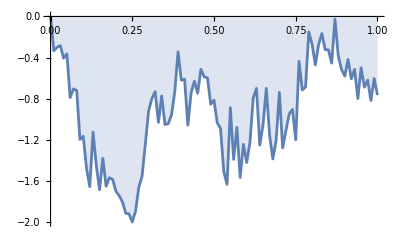

```mathematica
ListLinePlot[data, Filling->Axis]
```

```mathematica
Mean[FractionalBrownianMotionProcess[μ,σ,h][t]]
```

t μ

```mathematica
Variance[FractionalBrownianMotionProcess[μ,σ,h][t]]
```

t^(2 h) σ^2

```mathematica
CovarianceFunction[FractionalBrownianMotionProcess[μ,σ,h],s,t]
```

1/2 σ^2 (s^(2 h)+t^(2 h)-Abs[-s+t]^(2 h))

```mathematica
Plot3D[CovarianceFunction[FractionalBrownianMotionProcess[1/3],s,t],{s,0,5},{t,0,5}, ColorFunction->"Rainbow"]
```

-Graphics3D-